# Sagnac Gravitational Wave Detector (or not!)

## Cavity Equations

```mathematica
$Assumptions={t<1,t>0,L>0,f>0,Element[{t,L,f}, Reals]}
```

{t<1,t>0,t∈Reals}

### Constants

```mathematica
cLight=299792458; (* m/s *)
Tin=0.01;
Lin = 0.0001;
Len=4000;
```

### Signal gain in a cavity, relative to gain at DC

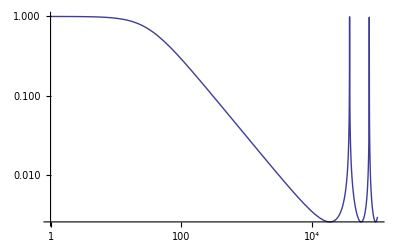

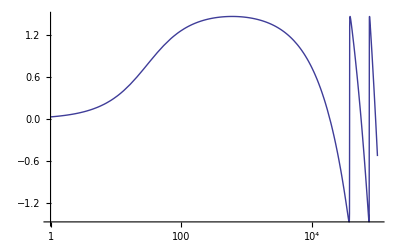

```mathematica
Gcav[T_,Loss_,L_,f_]:=(1-r)/(1-r Exp[I ϕ])/.{r->Sqrt[1-T-Loss],ϕ->4 π L f / cLight}
LogLogPlot[Abs[Gcav[Tin,Lin,Len,f]],{f,1,100000}]
LogLinearPlot[Arg[Gcav[Tin,Lin,Len,f]],{f,1,100000}]
```

### Cavity Amplitude Reflectivity

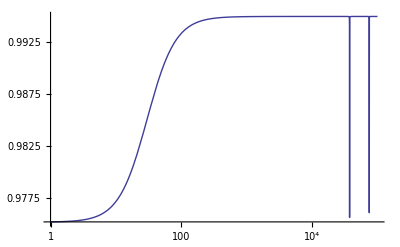

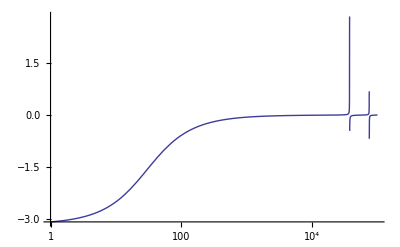

```mathematica
Rcav[T_,Loss_,L_,f_]:=1-T/(1-r Exp[I ϕ])/.{r->Sqrt[1-T-Loss],ϕ->4 π L f / cLight}
LogLogPlot[Abs[Rcav[Tin,Lin,Len,f]],{f,1,100000}]
LogLinearPlot[Arg[Rcav[Tin,Lin,Len,f]],{f,1,100000}]
```

### Arm to AS Port Signal Transfer

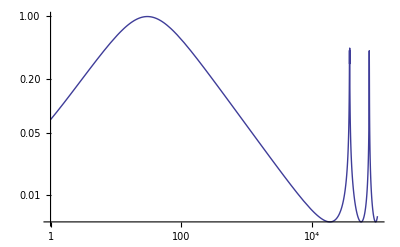

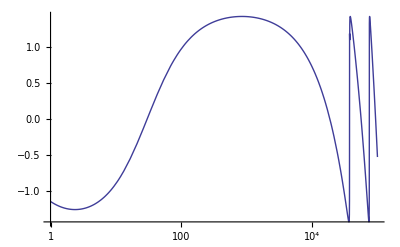

```mathematica
ArmAS[T_,Loss_,L_,f_]:=Gcav[T,Loss,L,f](1+Rcav[T,Loss,L,f])
LogLogPlot[Abs[ArmAS[Tin,Lin,Len,f]],{f,1,100000}]
LogLinearPlot[Arg[ArmAS[Tin,Lin,Len,f]],{f,1,100000}]
```